Silvesterovo pravidlo - grafické vykreslení
Autor: David Poledne
Datum: 6. května 2025

Popis:
Tento skript graficky vykresluje uzly silvesterova pravidla pro daný řád d na trojúhelníku s vrcholy vrchol1, vrchol2 , vrchol3.

Řád kvadratury: 3

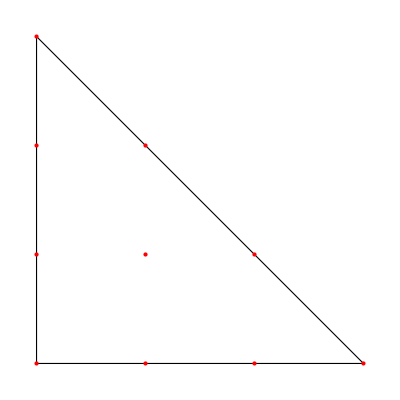

```mathematica
Remove["Global`*"]

(*Řád pravidla*)
d=3;

(*Trojúhelník přes který se integruje*)
vrchol1={0,0};
vrchol2={1,0};
vrchol3={0,1};
verticesPoints={vrchol1,vrchol2,vrchol3};

Row[{"Řád kvadratury: ",d}]
(*Všechny indexy kde k1+k2+k3=d*)
indexAll=Select[Flatten[Table[{i,j,k},{i,0,d},{j,0,d},{k,0,d}],2],Total[#]==d&];

(*Uzly*)
nodes=Table[{indexAll[[i]][[1]]vrchol1[[1]]/d+indexAll[[i]][[2]]vrchol2[[1]]/d+indexAll[[i]][[3]]vrchol3[[1]]/d,indexAll[[i]][[1]]vrchol1[[2]]/d+indexAll[[i]][[2]]vrchol2[[2]]/d+indexAll[[i]][[3]]vrchol3[[2]]/d},{i,1,Length[indexAll]}];

(*Grafické vykreslení uzlů*)
Graphics[{EdgeForm[Black],FaceForm[],Polygon[verticesPoints],Red,PointSize[Large],Point[nodes] }]
```